# AntonAntonov/MonadicContextualClassification

A monad for machine learning classification workflows

## Paclet Manifest

"Documentation"

"Kernel"

"ClCon.wl"KernelClCon.wl

"MonadicContextualClassification.wl"KernelMonadicContextualClassification.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image



### Basic Description

A paragraph that describes your paclet in more detail.

### Details

Additional information about the paclet.

### Primary Context

AntonAntonov`MonadicContextualClassification`

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["AntonAntonov`MonadicContextualClassification`"];
```

### Basic Examples

Here is a dataset:

```mathematica
dsTitanic=ResourceFunction["ExampleDataset"][{"MachineLearning","Titanic"}];
dsTitanic⟦100;;108;;2⟧
```

Here is a classification pipeline:

summaries:  {trainingData→{1 passenger class
3rd | 533
1st | 248
2nd | 200,2 passenger age
Min | 0.1667
1st Qu | 20.625
Median | 28.
Mean | 29.7189
3rd Qu | 39.
Max | 80.
Missing[___] | 182,3 passenger sex
male | 634
female | 347,4 passenger survival
died | 606
survived | 375},testData→{1 passenger class
3rd | 176
2nd | 77
1st | 75,2 passenger age
Min | 0.75
1st Qu | 22.
Median | 28.5
Mean | 30.4059
3rd Qu | 38.
Max | 76.
Missing[___] | 81,3 passenger sex
male | 209
female | 119,4 passenger survival
died | 203
survived | 125}}

value:  <|Accuracy→0.805668,Precision→<|died→0.770588,survived→0.883117|>,Recall→<|died→0.935714,survived→0.635514|>|>

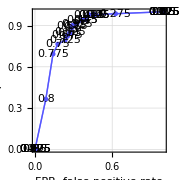
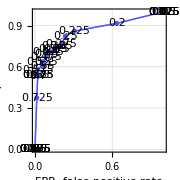
ROC plot(s):  <|died→-Graphics-,survived→-Graphics-|>

ClCon[<|died -> -Graphics-, survived -> -Graphics-|>, <|trainingData -> Dataset[{<|passenger class -> 2nd, passenger age -> 30., passenger sex -> female, passenger survival -> survived|>, <|passenger class -> 3rd, «2», passenger survival -> survived|>, «978», <|passenger class -> 3rd, passenger age -> 2., passenger sex -> female, passenger survival -> died|>}, «1», <||>], «3»|>]

```mathematica
clObj=
ClCon[dsTitanic,<||>]⟹
ClConSplitData[0.75]⟹
ClConEchoDataSummary⟹
ClConMakeClassifier["RandomForest"]⟹
ClConClassifierMeasurements[{"Accuracy","Precision","Recall"}]⟹
ClConEchoValue⟹
ClConROCPlot
```

### Scope

## Source & Additional Information

### Creator

Anton Antonov

### Source Control Repository

https://github.com/antononcube/WL-MonadicContextualClassification-paclet

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

ClCon

Classification

Classifier measurements

Machine Learning

Workflow

Data Science

ROC functions

ROC

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

AntonAntonov/ClassifierEnsembles

AntonAntonov/DataReshapers

AntonAntonov/MonadMakers

AntonAntonov/SSparseMatrix

AntonAntonov/OutlierIdentifiers

AntonAntonov/ROCFunctions

AntonAntonov/VariableImportanceByClassifiers

### Original Source References and Attributions

A monad for classification workflows | Mathematica for prediction algorithms

### Links

MathematicaForPrediction/MonadicProgramming/MonadicContextualClassification.m at master · antononcube/MathematicaForPrediction · GitHub

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.